```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zack/Documents/ignition/cantera/ratematrix

```mathematica
(* Benchmark scipy's eigenvalues and mathematica's. Sort the eigenvalues and eigenvectors in python before outputting..*)
```

```mathematica
filebase="data/h2o2test"
dat=Import[filebase<>"out.dat"];
{temp,press, atoms, dim,runtime} = dat[[-2,1;;5]]
elements=dat[[-1]];
file=OpenRead[filebase<>"ratematrix.npy","BinaryFormat"->True];
A=Transpose[Partition[BinaryReadList[file,"Real64"][[17;;-1]],dim]];
Close[file];
file=OpenRead[filebase<>"eigenvalues.npy","BinaryFormat"->True];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[file,"Real64"][[17;;-1]],2];
Close[file];
file=OpenRead[filebase<>"eigenvectors.npy","BinaryFormat"->True];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[file,"Real64"][[17;;-1]],2],dim];
Close[file];
file=OpenRead[filebase<>"spatoms.npy","BinaryFormat"->True];
spatoms=Partition[BinaryReadList[file,"Integer64"][[17;;-1]],Length[elements]];
Close[file];
file=OpenRead[filebase<>"multiindices.npy","BinaryFormat"->True];
multiindices=Partition[BinaryReadList[file,"Integer64"][[17;;-1]],Length[spatoms]];
Close[file];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,Subscript[elements[[j]],spatoms[[i,j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
multiforms=Table[Total[multiindices[[i]]*spforms],{i,1,dim}];
p=Grid[{{MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,10},{65,65}}],ListPlot[{Re[#]/Max[Abs[evals]],Im[#]/Max[Abs[evals]]}&/@evals,ImageSize->350,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{DisplayForm[RowBox[{Im[Subscript[λ,i]],"/",PaddedForm[Max[Abs[evals]],3]}]],None},{DisplayForm[RowBox[{Re[Subscript[λ,i]],"/",PaddedForm[Max[Abs[evals]],3]}]],Eigenvalues}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,10},{65,65}}]},{MatrixPlot[Reverse[evecs],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,10},{65,65}}],ListPlot[Abs[evecs[[-1]]],ImageSize->350,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,10},{65,65}}]}}]
Export["plots/example.pdf",p]
multiforms[[Reverse[Ordering[Abs[Eigensystem[A][[2,-1]]]]]]]
```

data/h2o2test

{1500,1,26,943,4.3943}

## Runtimes

{{9,19,0.0115093,332,9},{12,48,0.0813439,1225,12},{15,89,0.596218,3588,15},{18,177,4.28785,9583,18},{21,298,24.6733,22616,21},{24,516,133.293,50049,24},{27,807,644.169,102480,27}}

{{36,2803,3.06788,661388,36},{9,19,0.00170795,332,9},{12,48,0.00387898,1225,12},{15,89,0.0102981,3588,15},{18,177,0.0286813,9583,18},{21,298,0.0732696,22616,21},{24,516,0.173361,50049,24},{27,807,0.389899,102480,27},{30,1277,0.80559,200145,30},{33,1888,1.5921,370476,33},{36,2803,3.16585,661388,36}}

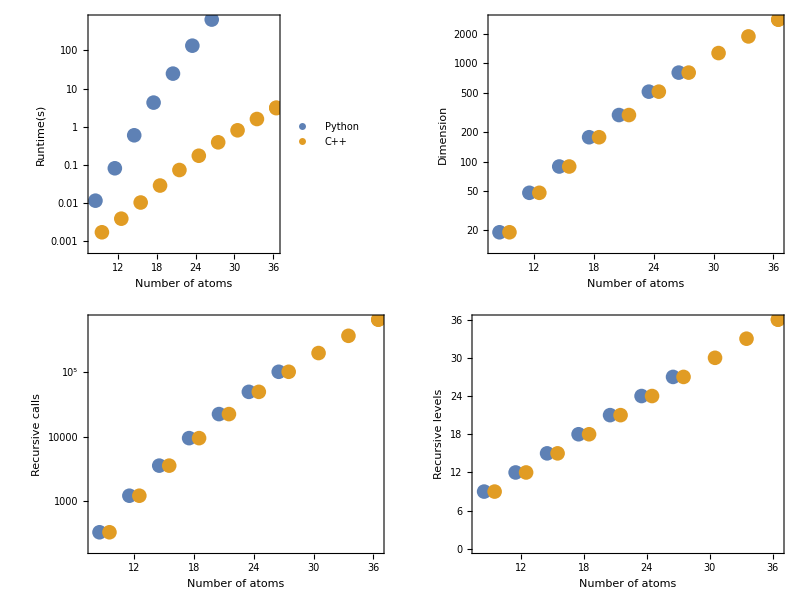

plots/runtimes.pdf

```mathematica
dat=Import["data/runtimesout.dat"]
dat2=Import["data/runtimes2out.dat"]
p=Legended[Grid[{{ListLogPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,3}]],{#[[1]]+0.5,#[[2]]}&/@dat2[[All,{1,3}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Runtime(s)"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]],ListLogPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,2}]],{#[[1]]+0.5,#[[2]]}&/@dat2[[All,{1,2}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Dimension"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]]},{ListLogPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,4}]],{#[[1]]+0.5,#[[2]]}&/@dat2[[All,{1,4}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive calls"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]],ListPlot[{{#[[1]]-0.5,#[[2]]}&/@dat[[All,{1,5}]],{#[[1]]+0.5,#[[2]]}&/@dat2[[All,{1,5}]]},ImageSize->350,AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive levels"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black],PlotStyle->Directive[PointSize[0.03]]]}}],Placed[PointLegend[ColorData[97,"ColorList"][[1;;2]],{"Python","C++"},LegendMarkerSize->20],Right]]
Export["plots/runtimes.pdf",p]
```

## Temperature - pressure sweep

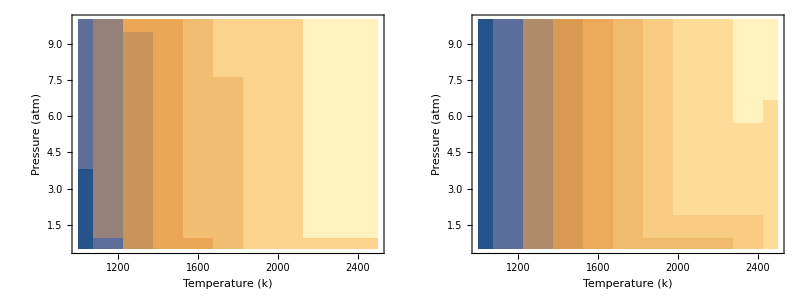

plots/sweep.pdf

```mathematica
sweep=Import["data/sweepout.dat"];
p=Grid[{{ListContourPlot[{#[[1]],#[[2]],Log[-#[[-2]]]}&/@sweep,ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Pressure (atm)",None},{"Temperature (k)",Log[-Subscript[λ,1]]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],InterpolationOrder->0],ListContourPlot[{#[[1]],#[[2]],Log[-#[[-3]]]}&/@sweep,ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{"Pressure (atm)",None},{"Temperature (k)",Log[-Subscript[λ,2]]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],InterpolationOrder->0]}}]
Export["plots/sweep.pdf",p]
```

## Temperature - atoms sweep

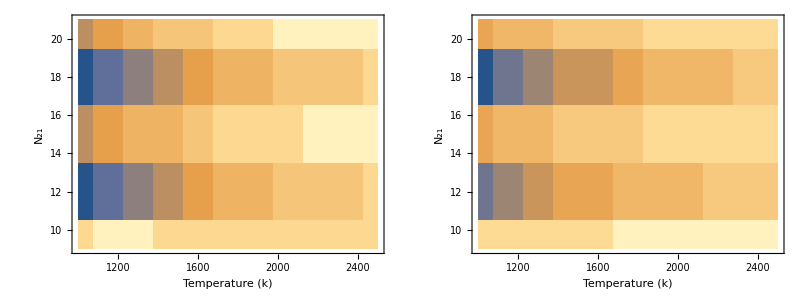

plots/sweep2.pdf

```mathematica
sweep2=Import["data/sweep2out.dat"];
p=Grid[{{ListContourPlot[{#[[1]],#[[3]],Log[-#[[-2]]]}&/@sweep2,ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{Subscript[N,atoms],None},{"Temperature (k)",Log[-Subscript[λ,1]]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],InterpolationOrder->0,PlotRange->All],ListContourPlot[{#[[1]],#[[3]],Log[-#[[-3]]]}&/@sweep2,ImageSize->350,LabelStyle->Directive[16,Black],FrameLabel->{{Subscript[N,atoms],None},{"Temperature (k)",Log[-Subscript[λ,2]]}},FrameStyle->Directive[Black,AbsoluteThickness[2]],InterpolationOrder->0,PlotRange->All]}}]
Export["plots/sweep2.pdf",p]
```